# Simulating Hybrid Electronic-Chemical Computer : Prime Factorization

#### Abhishek Sharma Cronin Lab University of Glasgow abhishek.sharma@glasgow.ac.uk

```mathematica
ClearAll["Global`*"]
```

```mathematica
baseDirectory=NotebookDirectory[]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\

## Problem Definition : Ising/QUBO formulation for Prime Factorization Problem

```mathematica
SeedRandom[110] (* Setting Seed for Random Number Generation *)
```

RandomGeneratorState[…]

Consider a l-bit integer N=p×q where p and q are the prime numbers. This factorization problem can be described as an optimization problem by defining the function f(x,y)=(N-x y)^2 where variables x and y are positive integers. Using [1], the number of bits required for n_x and n_y are given by,

n_x= m(⌊√N⌋_o) -1<= ⌊(l+1)/2⌋-1
n_y= m(⌊N/3⌋) -1<= l-1

[1] Quantum Adiabatic Algorithm for Factorization and Its Experimental Implementation, Phys. Rev. Lett. 101, 220405
[2] Quantum Annealing for Prime Factorization,  Sci Rep 8, 17667 (2018)

```mathematica
num=21; (* Number for the Prime Factorization *)
```

```mathematica
nX[num_]:= With[{fsqnum=Floor[√num]},Length@IntegerDigits[If[OddQ[fsqnum],fsqnum,fsqnum-1],2]-1];
nY[num_]:= With[{fsqnum=Floor[num/3]},Length@IntegerDigits[fsqnum,2]-1];
totalStates[num_]:=nX[num]+nY[num];
```

```mathematica
nQ[num_]:=Table[Symbol["x"<>ToString[i]],{i,totalStates[num]}];(* Defining spins as symbols for Ising Model Formulation *)
```

```mathematica
varsX=nQ[num][[1;;nX[num]]]; (* Spin variables for first number *)
varsY=nQ[num][[nX[num]+1;;totalStates[num]]]; (* Spin variables for second number *)
varsAll=Flatten@{varsX,varsY}
```

{x1,x2,x3}

```mathematica
pN=1+Total@Table[varsX[[i]] 2^i,{i,Length@varsX}]
```

1+2 x1

```mathematica
qN=1+Total@Table[varsY[[i]] 2^i,{i,Length@varsY}]
```

1+2 x2+4 x3

```mathematica
Ham=Expand[FullSimplify[(num-pN qN)^2]]
```

400-80 x1+4 x1^2-80 x2-152 x1 x2+16 x1^2 x2+4 x2^2+16 x1 x2^2+16 x1^2 x2^2-160 x3-304 x1 x3+32 x1^2 x3+16 x2 x3+64 x1 x2 x3+64 x1^2 x2 x3+16 x3^2+64 x1 x3^2+64 x1^2 x3^2

```mathematica
HamN=Ham/.((#^2->#)&/@varsAll)
```

400-76 x1-76 x2-104 x1 x2-144 x3-144 x1 x3+16 x2 x3+128 x1 x2 x3

```mathematica
rule[{xa_,xb_,xc_},xd_]:= xa xb xc ->xc xd +2(xa xb-2 xa xd-2xb xd +3xd)
```

```mathematica
rulesComb=Subsets[varsAll,{3}]
```

{{x1,x2,x3}}

```mathematica
rulesList=Table[rule[rulesComb[[i]],ToExpression["y"<>ToString[i]]],{i,Length@rulesComb}];
```

```mathematica
Expand[HamN/.rulesList]
```

400-76 x1-76 x2+152 x1 x2-144 x3-144 x1 x3+16 x2 x3+768 y1-512 x1 y1-512 x2 y1+128 x3 y1

```mathematica
rule=x1 x2 x3-> x4 x3 + 2(x1 x2 -2 x1 x4 -2 x2 x4 +3x4)
```

x1 x2 x3→x3 x4+2 (x1 x2+3 x4-2 x1 x4-2 x2 x4)

```mathematica
QuboToIsingRule=Block[{n,s},Table[Symbol["x"<>ToString[i]]->1/2 (1-Symbol[("s"<>ToString[i])]),{i,Length@nQ[num]+1}]] (* Rule for converting Ising to QUBO *)
```

{x1→(1-s1)/2,x2→(1-s2)/2,x3→(1-s3)/2,x4→(1-s4)/2}

```mathematica
HamF=Expand[FullSimplify[HamN/.rule]/.QuboToIsingRule]
```

418+164 s1+124 s2+38 s1 s2+72 s3-36 s1 s3+4 s2 s3-160 s4-128 s1 s4-128 s2 s4+32 s3 s4

```mathematica
nS={s1,s2,s3,s4}
```

{s1,s2,s3,s4}

```mathematica
quadTerms=Union[#⟦1⟧ #⟦2⟧&/@Tuples[nS,{2}]] (* Collecting Quadratic Terms *)
```

{s1^2,s1 s2,s2^2,s1 s3,s2 s3,s3^2,s1 s4,s2 s4,s3 s4,s4^2}

```mathematica
c2=Coefficient[HamF,quadTerms] (* Getting coefficients of all the quadratic terms *)
```

{0,38,0,-36,4,0,-128,-128,32,0}

```mathematica
linearTerms=HamF-Coefficient[HamF,quadTerms].quadTerms (* Getting coefficients of all linear terms *)
```

418+164 s1+124 s2+72 s3-160 s4

```mathematica
p=Coefficient[linearTerms,nS].Evaluate[#^2&/@nS] (* Changing linear terms to quadratic terms *)
```

164 s1^2+124 s2^2+72 s3^2-160 s4^2

```mathematica
q=c2.quadTerms (* Initial Quadratic Terms *)
```

38 s1 s2-36 s1 s3+4 s2 s3-128 s1 s4-128 s2 s4+32 s3 s4

```mathematica
offSet=First@Cases[Ham,_Integer] (* Offset term *)
```

400

```mathematica
HamQUBO=Expand[p+q+offSet](* Adding all terms and getting the full Hamiltonian for QUBO formulation *)
```

400+164 s1^2+38 s1 s2+124 s2^2-36 s1 s3+4 s2 s3+72 s3^2-128 s1 s4-128 s2 s4+32 s3 s4-160 s4^2

```mathematica
HamQUBO0 = offSet
```

400

```mathematica
HamQUBO1=Coefficient[HamQUBO,Evaluate[#^2&/@nS]]
```

{164,124,72,-160}

```mathematica
rules=Flatten@MapThread[{#1->#2}&,{quadTerms,Coefficient[HamQUBO,quadTerms]}]
```

{s1^2→164,s1 s2→38,s2^2→124,s1 s3→-36,s2 s3→4,s3^2→72,s1 s4→-128,s2 s4→-128,s3 s4→32,s4^2→-160}

```mathematica
selfInteraction=Block[{mat=Evaluate[#^2&/@nS]},MapThread[{#1,#2}&,{mat, Evaluate[mat/.rules]}]]
```

{{s1^2,164},{s2^2,124},{s3^2,72},{s4^2,-160}}

```mathematica
pairInteraction=Block[{mat=Union[#⟦1⟧ #⟦2⟧&/@Permutations[nS,{2}]],matCoeff},
matCoeff=ToExpression[StringSplit[ToString[#],"s"]]&/@mat;
MapThread[{#1,#2}&,{matCoeff, Evaluate[mat/.rules]}]]
```

{{{1,2},38},{{1,3},-36},{{2,3},4},{{1,4},-128},{{2,4},-128},{{3,4},32}}

Creating a two dimensional matrix to describe the fully coupled neighbour-neighbour interaction

```mathematica
twoPairArray=ConstantArray[0,{Length[nS],Length[nS]}];
```

```mathematica
(twoPairArray⟦#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧⟧=1/2#⟦2⟧)&/@pairInteraction;
```

```mathematica
twoPairArrayF=twoPairArray+ Transpose[twoPairArray];twoPairArrayF//MatrixForm
```

(0 | 19 | -18 | -64
19 | 0 | 2 | -64
-18 | 2 | 0 | 16
-64 | -64 | 16 | 0)

```mathematica
HamQUBO2=twoPairArrayF;HamQUBO2//MatrixForm (* Factorizing out the greatest common divisor *)
```

(0 | 19 | -18 | -64
19 | 0 | 2 | -64
-18 | 2 | 0 | 16
-64 | -64 | 16 | 0)

```mathematica
totalMat =DiagonalMatrix[HamQUBO1]+ twoPairArrayF;totalMat//MatrixForm
```

(164 | 19 | -18 | -64
19 | 124 | 2 | -64
-18 | 2 | 72 | 16
-64 | -64 | 16 | -160)

```mathematica
(1/(PolynomialGCD@@Flatten[totalMat])totalMat)//MatrixForm
```

(164 | 19 | -18 | -64
19 | 124 | 2 | -64
-18 | 2 | 72 | 16
-64 | -64 | 16 | -160)

## Initializing Droplet Array based on Computational Problem Formulation

#### Physical Constants

```mathematica
e=UnitConvert[Quantity["ElementaryCharge"]]; (* Electronic Charge *)
```

```mathematica
NA=UnitConvert[Quantity["AvogadroConstant"]]; (* Avogadro's Constant *)
```

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]]; (* Boltzmann's Constant *)
```

```mathematica
F=UnitConvert[Quantity["FaradayConstant"]]; (* Faraday's Constant *)
```

```mathematica
R=UnitConvert[Quantity["MolarGasConstant"]]; (* Molar Gas Constant *)
```

```mathematica
ϵ0=UnitConvert[Quantity["VacuumPermittivity"]];(* Vacuum Permittivity *)
```

```mathematica
T=Quantity[298.,"K"]; (* Working Temperature *)
```

#### Basic design and chemistry parameters

```mathematica
elecRadius=UnitConvert@Quantity[500.0,"micron"]; (* Radius of electrode *)
```

```mathematica
elecGap=UnitConvert@Quantity[1000.0,"microns"];(* Gap between two nearby electrodes *)
```

```mathematica
dropHeight=UnitConvert@Quantity[500.0,"microns"]; (* Height of the droplet above electrode array *)
```

```mathematica
dropletVolume = UnitConvert[(elecRadius+elecGap/2.)^2 dropHeight,"m^3"];(* Volume of the droplet based on the height and electrode dimensions *)
```

```mathematica
Cdl=UnitConvert@Quantity[0.02,"F/m^2"];(* Double Layer capacitance per unit area *)
```

```mathematica
CBack=UnitConvert@Quantity[300 10^-3,"Molar"]; (* Concentration of background supporting electrolyte *)
```

```mathematica
CEl=UnitConvert@Quantity[100 10^-3,"Molar"]; (* Concentration of electroactive species *)
```

```mathematica
𝒟=UnitConvert@Quantity[1 10^-9,"m^2/s"]; (* Diffusion constant of supporting electrolyte *)
```

```mathematica
𝒟ϵ=UnitConvert@Quantity[0.7 10^-9,"m^2/s"]; (* Diffusion constant of electroactive system *)
```

```mathematica
khom=UnitConvert@Quantity[2.5 10^-6,"m/s"];(* Homogeneous rate constant for the chemical reaction *)
```

```mathematica
z=1;(* Valence of background supporting electrolyte *)
```

```mathematica
BulkCond= (2 z^2 e^2 CBack NA 𝒟)/(kB T)//UnitSimplify (* Bulk Electrolytic Conductivity *)
```

2.25436 per meterper ohm

```mathematica
dropletBulkR1= 1/BulkCond elecGap/dropHeight^2
```

1774.34 Ω

```mathematica
dropletBulkR = 1/BulkCond(2dropHeight)/elecGap^2
```

443.585 Ω

```mathematica
iLim= UnitConvert[F 𝒟ϵ CBack/elecGap,"A/m^2"]; (* Limiting current density *)
```

```mathematica
limitingCurrent =UnitConvert[π elecRadius^2 F 𝒟ϵ CBack/elecGap,"A"] (* Diffusion limited current flowing through the electrode *)
```

0.0000159137 A

```mathematica
j0[cOx_,cRe_,k0_]:= F k0 cOx^β cRe^(1-β)
```

```mathematica
ExCurrentDensity =UnitConvert[ UnitSimplify[j0[CEl,CEl,khom]],"A/m^2"]
```

24.1213 A/m^2

```mathematica
ExCurrentDensity/iLim
```

1.19048

#### Phosphate Buffer Kinetics Parameters

```mathematica
eq1=K1==(Hp PO4)/HPO4;
```

```mathematica
eq2=K2==(Hp HPO4)/H2PO4;
```

```mathematica
eq3=K3==(Hp H2PO4)/H3PO4;
```

```mathematica
eq4=PO4+HPO4+H2PO4+H3PO4==iHPO4;
```

```mathematica
sol1=Solve[{eq1,eq2,eq3,eq4},{PO4,HPO4,H2PO4,H3PO4}];
```

```mathematica
{PO4,HPO4,H2PO4,H3PO4}/.sol1//Flatten
```

{(iHPO4 K1 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp iHPO4 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^2 iHPO4 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^3 iHPO4)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3)}

```mathematica
totalPhosphate= Quantity[30 10^-3,"Molar"]; (* Total Phosphate Concentration *)
```

```mathematica
pK3 = 2.15; (* Phosphate Buffer pK3 *)
```

```mathematica
pK2=7.2; (* Phosphate Buffer pK2 *)
```

```mathematica
pK1= 12.35; (* Phosphate Buffer pK1 *)
```

```mathematica
quant = {iHPO4-> totalPhosphate,K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}; (* Assuming initial pH is 7 *)
```

```mathematica
quant2=Hp-> Quantity[10^-8,"Molar"];
```

So, initial percent of all the species :

```mathematica
({PO4,HPO4,H2PO4,H3PO4}/iHPO4)/.sol1/.quant/.quant2//Flatten
```

{0.0000385559,0.86316,0.136802,1.93237×10^-7}

```mathematica
{icA,icB,icC,icD}={PO4,HPO4,H2PO4,H3PO4}/.sol1/.quant/.quant2//Flatten
```

{1.15668×10^-6 M,0.0258948 M,0.00410405 M,5.79712×10^-9 M}

```mathematica
Unprotect[$MachinePrecision];
$MachinePrecision=50; (* Necessary for better precision for numerical stability in pH calculations *)
Protect[$MachinePrecision];
```

```mathematica
icAM = QuantityMagnitude@icA;icBM = QuantityMagnitude@icB;icCM = QuantityMagnitude@icC;icDM = QuantityMagnitude@icD;
```

```mathematica
pHdropletUpdate[appC_,Δt_,{cA_,cB_,cC_,cD_}]:=Module[{eqn1,eqn2,eqn3,eqn4,quant,soln,HpNC},
(*  
   -> appC : applied current 
 -> Δt : time interval
-> {cA, cB, cC, cD} : Input Concentration of four phosphate species 
*)
eqn1[cA,cB,cC,cD]:=K1==(Hp (cA-α HpN))/(cB +α HpN -β HpN);
eqn2[cA,cB,cC,cD]:=K2==(Hp (cB +α HpN -β HpN))/(cC+β HpN-γ HpN);
eqn3[cA,cB,cC,cD]:=K3==(Hp (cC+β HpN-γ HpN))/(cD+γ HpN);
eqn4=α+β+γ ==1.;
quant ={K3->10^-pK3,K2->10^-pK2,K1->10^-pK1}; 
HpNC=10^-3 QuantityMagnitude[(Quantity[appC,"Amperes"]Quantity[Δt,"s"])/(2 dropletVolume F)];  
(*Print[({eqn1[cA,cB,cC,cD],eqn2[cA,cB,cC,cD],eqn3[cA,cB,cC,cD],eqn4}/.HpN->HpNC/.quant)/.q_Quantity:>QuantityMagnitude[q]];*)
soln=NSolve[({eqn1[cA,cB,cC,cD],eqn2[cA,cB,cC,cD],eqn3[cA,cB,cC,cD],eqn4}/.HpN->HpNC/.quant)/.q_Quantity:>QuantityMagnitude[q],{Hp,α,β,γ},WorkingPrecision->100];Chop[{-Log[10,Hp],cA-α HpNC,cB +α HpNC -β HpNC,cC+β HpNC-γ HpNC,cD+γ HpNC}/.soln⟦3⟧]]
```

#### Governing equations for multi-electrode array network

Creates network equations for n x n droplet array with time dependent electrode potentials.

```mathematica
fVShift[{V1_,V2_},{λ_,t0_},t_]:=V1+(V2-V1)(1/2+1/π ArcTan[(t-t0)/λ]) (* Time dependent potential shift function *)
```

```mathematica
droplet2DBV[i_,j_,K_,tS_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==If[electrodeType⟦i,j⟧=="ACTIVE", AreaEL Cdl D[Evaluate[fVShift[{ Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0(Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/.ηm-> Evaluate[fVShift[{Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0]],leakageCurrent];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
droplet2DmBV[i_,j_,K_,t0_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==If[electrodeType⟦i,j⟧=="ACTIVE",AreaEL Cdl D[Evaluate[fVShift[{ Symbol["Vf"<>indexStr],Symbol["Vi"<>indexStr][t]},{λ,t0},t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0( (Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/(1+i0/iL(Exp[(αa F ηm)/(R T)]+Exp[-(αc F ηm)/(R T)])))/.ηm-> Evaluate[fVShift[{ Symbol["Vf"<>indexStr],Symbol["Vi"<>indexStr][t]},{λ,t0},t]-Symbol["ϕ"<>indexStr][t]-E0]],leakageCurrent];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
dropletConnections2D[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,vars}, 
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["iCN"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"N"][t];
eq2=Symbol["iCN"<>indexStr][t]==-Symbol["i"<>ToString[i]<>"s"<>ToString[j+1]<>"S"][t]; 
eq3=Symbol["iCE"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"E"][t];

eq4=Symbol["iCE"<>indexStr][t]==-Symbol["i"<>ToString[i+1]<>"s"<>ToString[j]<>"W"][t];
eq5=Symbol["ϕPN"<>indexStr][t]-Symbol["ϕPS"<>ToString[i]<>"s"<>ToString[j+1]][t]== RConn Symbol["iCN"<>indexStr][t];
eq6=Symbol["ϕPE"<>indexStr][t]-Symbol["ϕPW"<>ToString[i+1]<>"s"<>ToString[j]][t]== RConn Symbol["iCE"<>indexStr][t];

vars={Symbol["iCN"<>indexStr][t],Symbol["iCE"<>indexStr][t]};
{{eq1,eq2,eq3,eq4,eq5,eq6},vars}]
```

```mathematica
dropletEndConnections2D[K_]:=Module[{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14,vars},
(* --- Left Column --- *)
eqSet1=Table[Symbol["iCW1"<>"s"<>ToString[j]][t]==Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];
eqSet2=Table[Symbol["ϕP1"<>"s"<>ToString[j]][t]==RConn Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];

(* --- Bottom Row --- *)
eqSet3=Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t]==Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];
eqSet4=Table[Symbol["ϕP"<>ToString[j]<>"s"<>"1"][t]==RConn Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];

(* --- Right Column --- *)
eqSet5=Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];
eqSet6=Table[Symbol["ϕP"<>ToString[K]<>"s"<>ToString[j]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];

eqSet7=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];
eqSet8=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==-Symbol["i"<>ToString[K]<>"s"<>ToString[j+1]<>"S"][t],{j,1,K-1}];
eqSet9=Table[Symbol["ϕPN"<>ToString[K]<>"s"<>ToString[j]][t]-Symbol["ϕPS"<>ToString[K]<>"s"<>ToString[j+1]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];

(* --- Top Row --- *)
eqSet10=Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];
eqSet11=Table[Symbol["ϕP"<>ToString[j]<>"s"<>ToString[K]][t]==RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];

eqSet12=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];
eqSet13=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==-Symbol["i"<>ToString[j+1]<>"s"<>ToString[K]<>"W"][t],{j,1,K-1}];
eqSet14=Table[Symbol["ϕPE"<>ToString[j]<>"s"<>ToString[K]][t]-Symbol["ϕPW"<>ToString[j+1]<>"s"<>ToString[K]][t]== RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];

vars={Table[Symbol["iCW1"<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t],{j,1,K}],
           Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}],
           Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}]};
{{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14}//Flatten,vars//Flatten}]
```

```mathematica
eqns[N_,t0_]:=Flatten[Table[droplet2DBV[i,j,N,t0],{i,1,N},{j,1,N}],1] (* Electrochemical Kinetics Description *)
```

```mathematica
eqnsCon[N_]:=Flatten[Table[dropletConnections2D[i,j,N],{i,1,N-1},{j,1,N-1}],1] (* Connections between Droplets *)
```

```mathematica
eqnsEndCon[N_]:=dropletEndConnections2D[N] (* Connections between droplets at the boundaries *)
```

```mathematica
Clear[λ,tS,cAdroplet,cBdroplet,cCdroplet,cDdroplet,soln,solnS]
```

```mathematica
If[FileExistsQ[baseDirectory<>"LOG.txt"],DeleteFile[baseDirectory<>"LOG.txt"]] (* Removing old log file *)
```

```mathematica
logFile=CreateFile[baseDirectory<>"LOG.txt"] (* Records details of pH values and Ising states *)
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\LOG.txt

#### Parameters for pH based computational logic

```mathematica
offSet=0.25; (* Electrode Potential offset time for shifting *)
λ=10^-4; (* Parameter for sharpness of potential shift *)
tS=4.0; (* Time step for potential shift in seconds *) 
leakageCurrent = 1 10^-12; (* Leakage current on inactive electrodes in Amperes *)
vInit = 1 10^-6; (* Potential on inactive electrode in absense of applied potential for numerical stability *)
timeStep = 0.1; (* Time stepping for pH calculation in seconds *)
switchTime=60.0;(* Switch time between two pH states on the working electrode *)
appVoltage=1.0; (* Scaling factor for the applied voltage *)
αVoltage=0.1; (* Proportional factor for applied voltage based on pH difference *)
stateRange=0.2;(* pH range for computational state deviation ±0.25 *)
```

```mathematica
pHStateMin=4.0; (* Minimum pH state, equivalent to -1 of the abstract state *)
pHStateMax=11.0; (* Maximum pH state, equivalent to +1 of the abstract state *)
minpHShift=0.2; (* Minimum pH shift operation, to be controlled from electrode actuation *) 
totalStates=1/minpHShift (pHStateMax-pHStateMin); (* Total number of possible discrete states pH states / abstract states *)
absStateDiff= 2/totalStates; (* Difference between two nearest abstract space based on pH measurement limitation *)
```

```mathematica
pHstates=Table[pHStateMin+i minpHShift,{i,0,totalStates}] (* List all the possible pH states *)
```

{4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.}

```mathematica
abstractStates=Table[-1+i absStateDiff,{i,0,totalStates}] (* List all the possible abstract space equivalent to pH states *)
```

{-1.,-0.942857,-0.885714,-0.828571,-0.771429,-0.714286,-0.657143,-0.6,-0.542857,-0.485714,-0.428571,-0.371429,-0.314286,-0.257143,-0.2,-0.142857,-0.0857143,-0.0285714,0.0285714,0.0857143,0.142857,0.2,0.257143,0.314286,0.371429,0.428571,0.485714,0.542857,0.6,0.657143,0.714286,0.771429,0.828571,0.885714,0.942857,1.}

```mathematica
stateShift[state_]:=Block[{diff,minPos},diff=Abs@(state-#)&/@abstractStates;minPos=First@Position[diff,Min[diff]];First@abstractStates⟦minPos⟧]
```

```mathematica
nEl=7; (* Number of electrodes along X and Y *)
nElW =2; (* Number of working electrodes along X ans Y *)
```

```mathematica
Length@nS== nElW^2(* Checking if number of electrodes matches with number of spin variables *)
```

True

```mathematica
{icAM,icBM,icCM,icDM} (* Initial concentration of phosphate species in each droplet *)
```

{1.15668×10^-6,0.0258948,0.00410405,5.79712×10^-9}

```mathematica
(* Defining concentration of phosphate species on each droplet *)
cAdroplet=Table[icAM,{i,nEl},{j,nEl}]; 
cBdroplet=Table[icBM,{i,nEl},{j,nEl}]; 
cCdroplet=Table[icCM,{i,nEl},{j,nEl}];cDdroplet=Table[icDM,{i,nEl},{j,nEl}];
```

```mathematica
Clear[dataT];dataT= {};pHdiffRec={}; (* Empty array for storing pH values *)
```

```mathematica
(* Initializing all electrodes as INACTIVE *)
Clear[electrodeType]
electrodeType=Table["INACTIVE",{i,nEl},{j,nEl}];
```

```mathematica
(* Activating Working Electrodes *)
(*** MAKE SURE THIS IS CORRECT... COULD DIFFER FOR EVEN OR ODD NUMBER OF ELECTRODES, THIS IS FOR TEST ONLY (TO BE UPDATED) ***)
WE=Flatten[Table[{i,j},{i,Ceiling[nEl/2]-(Ceiling[nElW/2]),Ceiling[nEl/2]+(Ceiling[nElW/2]),2},{j,Ceiling[nEl/2]-(Ceiling[nElW/2]),Ceiling[nEl/2]+(Ceiling[nElW/2]),2}],1]
```

{{3,3},{3,5},{5,3},{5,5}}

```mathematica
(electrodeType⟦WE⟦#,1⟧,WE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[WE]];
```

```mathematica
(* Activating neighbouring Counter Electrodes *)
```

```mathematica
CE=Union[Flatten[Block[{elec=WE⟦#⟧},{{elec⟦1⟧+1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧+1},{elec⟦1⟧-1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧-1}}]&/@Range[Length[WE]],1]];
```

```mathematica
Show[{ListPlot[Flatten[Table[{i,j},{i,nEl},{j,nEl}],1],AspectRatio->1,Axes->True,BaselinePosition->Center,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,PointSize-> 0.04},Frame-> None,FrameTicks->None,AspectRatio->1],ListPlot[WE,PlotStyle->{Red,PointSize-> 0.04},AspectRatio->1,Axes->True,BaselinePosition->Center,Frame-> None,FrameTicks->None,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AspectRatio->1],ListPlot[CE,PlotStyle->{Blue,PointSize-> 0.04},AspectRatio->1,Axes->True,BaselinePosition->Center,Frame-> None,FrameTicks->None,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AspectRatio->1]},ImageSize-> Small,PlotRange->{{0,8},{0,8}}]; (* Uncomment to see the position of electrodes *)
```

```mathematica
(electrodeType⟦CE⟦#,1⟧,CE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[CE]];
```

```mathematica
(* Initializing potentials on all the electrodes*)
```

```mathematica
(* Finding neighbouring working electrodes around each counter electrode *)
```

```mathematica
NeighboursWE[ce_]:=Block[{eX=ce⟦1⟧,eY=ce⟦2⟧},{{eX+1,eY},{eX,eY+1},{eX-1,eY},{eX,eY-1}}]
```

```mathematica
neighbourlistWE=Table[Select[NeighboursWE[CE⟦i⟧],MemberQ[WE,#]&],{i,Length[CE]}];
```

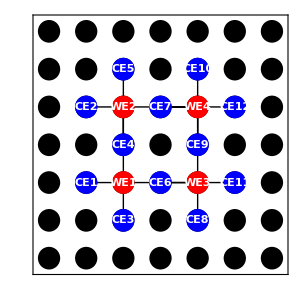

```mathematica
p0=Graphics[{Line[#]&/@Table[Flatten[MapThread[{#1,#2}&,{ConstantArray[CE[[i]],Length@neighbourlistWE[[i]]],neighbourlistWE[[i]]}],1],{i,Length@CE}],Flatten[Table[Disk[{i,j},0.3],{i,nEl},{j,nEl}],1],Flatten[{Red,Disk[#,0.3]}&/@WE],Flatten[{Blue,Disk[#,0.3]}&/@CE],White,Table[Text[Style["WE"<>ToString[i],Bold],WE[[i]]],{i,Length@WE}],Table[Text[Style["CE"<>ToString[i],Bold],CE[[i]]],{i,Length@CE}]},ImageSize->300,Frame->True,FrameTicks->None,ImageSize->300]
```

```mathematica
Export[baseDirectory<>"Electrode_Layout.png",p0,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\Electrode_Layout.png

```mathematica
potPatterns=Table[vInit,{i,nEl},{j,nEl}];
```

```mathematica
Table[Mean[potPatterns⟦#⟦1⟧,#⟦2⟧⟧&/@neighbourlistWE⟦i⟧],{i,Length[neighbourlistWE]}];
```

```mathematica
(* Setting scaled potentials on Working Electrodes *)
```

```mathematica
(*(potPatterns⟦WE⟦#,1⟧,WE⟦#,2⟧⟧=appVoltage)&/@Range[Length[WE]];*)
```

```mathematica
(* Setting pH states on all the working electrodes *)
```

```mathematica
(*(potPatterns⟦CE⟦#,1⟧,CE⟦#,2⟧⟧=-appVoltage)&/@Range[Length[CE]];*)
```

#### Ising/QUBO Minimization on Droplet Array with pH control logic (for Prime Factorization Problem)

```mathematica
(* Calculates the energy of the abstract states *)
calculateEnergy[state_,Ham0_,Ham1_,Ham2_]:= Module[{pairwise,singleTerms,coupledTerms},singleTerms=Total[state Ham1];
pairwise=Subsets[Range@Length[state],{2}];
coupledTerms=2.Total[(Ham2⟦#⟦1⟧,#⟦2⟧⟧&/@pairwise)(state⟦#⟦1⟧⟧state⟦#⟦2⟧⟧&/@pairwise)];
Ham0+singleTerms+coupledTerms]
```

```mathematica
(* Calculates the gradients to update the current state *)
calculateGradients[state_,Ham1_,Ham2_]:=Module[{singleTerms,coupledTerms,grad,m1,m2,ff,p1,p2},singleTerms=Ham1;
m1=DeleteCases[Range[Length@state],#]&/@Range[Length@state];
m2=ConstantArray[#,Length[state]-1]&/@Range[Length@state];
ff=MapThread[Transpose[{#1,#2}]&,{m1,m2}];
p1=Table[Ham2⟦#⟦1⟧,#⟦2⟧⟧&/@ff⟦i⟧,{i,Length@ff}];
p2=Table[state⟦#⟧&/@m1⟦i⟧,{i,Length@ff}];
coupledTerms=Table[p1⟦i⟧.p2⟦i⟧,{i,Length@p1}];
grad = singleTerms + 2 coupledTerms]
```

```mathematica
(* Updates the abstract states for pH control *)
updateStates[state_,fac_,Ham1_,Ham2_,noiseMax_]:=Module[{grad,gradCorrected,gradNorm,norm,rem=0,upState,upStateS},grad=calculateGradients[state,Ham1, Ham2];gradCorrected=Piecewise[{{0.,state⟦#⟧<-1+10^-8 && grad⟦#⟧>0},{0.,state⟦#⟧>1-10^-8 && grad⟦#⟧<0}},rem++;grad⟦#⟧]&/@Range[Length@grad];
gradNorm=If[Total[Abs[gradCorrected]]> 1 10^-10&&rem>0,norm=Total[Abs[gradCorrected]]/rem;gradCorrected/norm,grad];
upState=Piecewise[{{1,#>1},{-1.,#<-1}},#]&/@(state- RandomReal[{-noiseMax/2,noiseMax/2},Length@nS]-fac (gradNorm));
stateShift[#]&/@upState]
```

```mathematica
stateShift[state_]:=Block[{diff,minPos},diff=Abs@(state-#)&/@abstractStates;minPos=First@Position[diff,Min[diff]];First@abstractStates⟦minPos⟧]
```

```mathematica
energySys={}; (* Keeps Track of the energy of the system *)
```

```mathematica
(* Complete function to electrochemical automata of the droplet array *)
electroChemAutomata[N_,nTs_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataPlot,dataC,soln,cAdropletC,cBdropletC,cCdropletC,cDdropletC,initStates,initpH,stateAbs,currentpH,setpHe,pHdiff,cePotentials},
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2];
params={AreaEL-> UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
cnTs=0;Vapp={}; solnS={}; 

(* Initializing Concentrations of Phosphate species*)
cAdropletC=cAdroplet;
cBdropletC=cBdroplet;
cCdropletC=cCdroplet;
cDdropletC=cDdroplet;

(* Initializing abstract states and equivalent pH states *)
initStates = stateShift[#]&/@RandomReal[{-0.5,0.5},Length@nS]; (* Setting initial abstract space *)
stateAbs=initStates;
initpH=(pHStateMin+((pHStateMax-pHStateMin)/2)(#+1))&/@initStates;
setpHe=initpH; (* Setting initial pH states *)
PrintTemporary["Initial Abstract space : ",stateAbs];
PrintTemporary["Initial pH states : ",initpH];

While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
PrintTemporary["-------------------------------------------------------------"];
PrintTemporary["Current Switching Step : ", cnTs, "; Current Time : ", cnTs tS];

WriteLine[logFile,"-------------------------------------------------------------"];
WriteLine[logFile,"Current Switching Step : "<>ToString[ cnTs]<> "; Current Time : "<> ToString[cnTs tS]];

(* Randomly selecting pH states on all working electrodes *)
If[Mod[Quotient[cnTs tS,switchTime],2] ≠  Mod[Quotient[(cnTs-1) tS,switchTime],2],
(* Update Abstract states *)
stateAbs=updateStates[stateAbs,0.2,HamQUBO1,HamQUBO2,0.5];
Print["Energy : ",calculateEnergy[stateAbs,HamQUBO0,HamQUBO1,HamQUBO2]];
energySys= Join[energySys,{calculateEnergy[stateAbs,HamQUBO0,HamQUBO1,HamQUBO2]}];
(* Update pH states *)
setpHe=(pHStateMin+((pHStateMax-pHStateMin)/2)(#+1))&/@stateAbs;
(*
pHstates= RandomChoice[{-1,1},Length[WE]];
setpHe=Table[If[pHstates⟦i⟧== 1,pHstate1,pHstate2]
,{i,Length[WE]}];
*)
PrintTemporary["****** SWITCHING TO NEW STATES ******"]];PrintTemporary["Current abstract computational states : ", stateAbs];
PrintTemporary["Current pH states : ", setpHe];
(*
WriteLine[logFile,"Current abstract computational states : "<>ToString[pHstates]];
WriteLine[logFile,"Current pH states : "<>ToString[setpHe]];
*)

Which[cnTs== 0 ,
(* Set initial potential on all the electrodes at t=0 *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}],

cnTs≠ 0 ,
(* At any other time step *)
(* Setting potentials on working electrodes, proportional to pH difference *)
(potPatterns⟦WE⟦#,1⟧,WE⟦#,2⟧⟧=-αVoltage pHdiff⟦#⟧)&/@Range[Length[WE]];

(* Setting counter electrode potentials based on neighbouring working electrodes *)
cePotentials=Table[Mean[potPatterns⟦#⟦1⟧,#⟦2⟧⟧&/@neighbourlistWE⟦i⟧],{i,Length[neighbourlistWE]}];
(potPatterns⟦CE⟦#,1⟧,CE⟦#,2⟧⟧=-cePotentials⟦#⟧)&/@Range[Length[CE]];

params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->potPatterns⟦i,j⟧),{i,1,N},{j,1,N}]//Flatten;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}]];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
Monitor[soln=Quiet[NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^5,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)]],step];
solnS=Join[solnS,soln];

(* Updating pH on each droplet *)
currentEL=Flatten[Table[Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.soln]/.t-> tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],1];
PrintTemporary[Table[tC,{tC,tS cnTs, tS (cnTs+1),timeStep}]];
dim=Dimensions[currentEL]; 
PrintTemporary[dim];
dataC=ParallelTable[Block[{dat=currentEL⟦All,p,q⟧},
Quiet[Monitor[Table[Block[{out},
out=pHdropletUpdate[dat⟦i⟧,timeStep,{cAdropletC⟦p,q⟧,cBdropletC⟦p,q⟧,cCdropletC⟦p,q⟧,cDdropletC⟦p,q⟧}];
cAdropletC⟦p,q⟧=out⟦2⟧;
cBdropletC⟦p,q⟧=out⟦3⟧;
cCdropletC⟦p,q⟧=out⟦4⟧;
cDdropletC⟦p,q⟧=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];
currentpH=(dataC⟦WE⟦#,1⟧,WE⟦#,2⟧,tS/timeStep+1⟧⟦1⟧)&/@Range[Length[WE]];
pHdiff=(setpHe-currentpH);

pHdiffRec=Join[pHdiffRec,{pHdiff}];
dataT=Join[dataT,{dataC}];
PrintTemporary["Current Measured pHs : ",NumberForm[currentpH,3]];
PrintTemporary["Current pH differences : ",NumberForm[pHdiff,3]];
PrintTemporary["pH state STATUS : ",If[Abs[pHdiff⟦#⟧]≤ stateRange/2. ,"A","NA"]&/@Range[Length[pHdiff]]];

WriteLine[logFile,"Current Measured pHs : "<>ToString[NumberForm[currentpH,3]]];
WriteLine[logFile,"Current pH differences : "<>ToString[NumberForm[pHdiff,3]]];
WriteLine[logFile,"pH state STATUS : "<>ToString[If[Abs[pHdiff⟦#⟧]≤ stateRange/2. ,"A","NA"]&/@Range[Length[pHdiff]]]];
cnTs=cnTs+1]];
```

Running Simulation

```mathematica
cnTs=0;nSteps=300;
electroChemAutomata[nEl,nSteps]
```

Energy : 312.24

Energy : 250.803

Energy : 187.704

Energy : 123.44

Energy : 104.322

Energy : 65.5788

Energy : 32.0637

Energy : 100.273

Energy : -1.54286

Energy : 18.

Energy : 59.1853

Energy : -18.

Energy : -18.

Energy : -18.

«6 more identical outputs»

```mathematica
Dimensions@dataT
```

{301,7,7,41,5}

```mathematica
plotStyle=MapThread[{#1,#2,#3}&,{ConstantArray[PointSize[0.005],Length@WE],ConstantArray[Opacity[0.4],Length@WE],ColorData[16,#]&/@Range[Length@WE]}];
```

```mathematica
timeList=Range[0.1,(nSteps +1)tS ,timeStep];
```

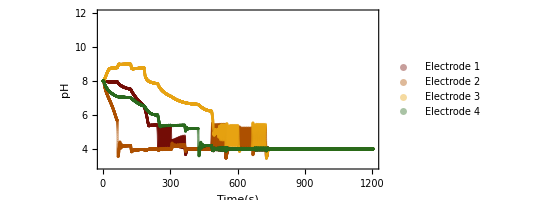

```mathematica
p1=ListPlot[Table[MapThread[{#1,#2}&,{timeList,Flatten[(dataT⟦All,WE⟦#,1⟧,WE⟦#,2⟧,1;;IntegerPart@(tS/timeStep)⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,4}],PlotStyle->plotStyle,AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time(s)","pH"},PlotRange-> {All,{3,12}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.8,0.6}],ImageSize->400]
```

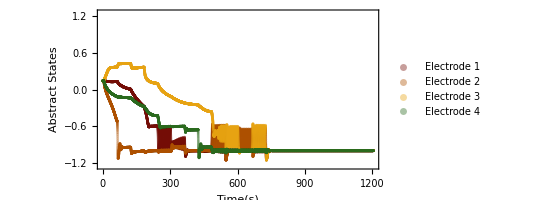

```mathematica
p2=Block[{data=Table[Flatten[(dataT⟦All,WE⟦#,1⟧,WE⟦#,2⟧,1;;IntegerPart@(tS/timeStep)⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,4}],dataX},
dataX=(-1+2/(pHStateMax-pHStateMin) (#-pHStateMin))&/@data;
ListPlot[Table[MapThread[{#1,#2}&,{timeList,dataX[[i]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,FrameLabel-> {"Time(s)","Abstract States"},PlotRange-> {All,{-1.25,1.25}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.8,0.6}],ImageSize->400]]
```

```mathematica
plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
```

```mathematica
dataVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
voltageData=Table[plotVoltage[nEl,t],{t,0.1,1200,0.1}];
dataX=Table[voltageData[[All,WE[[i,1]],WE[[i,2]]]],{i,Length@WE}];
```

```mathematica
timeList=Range[0.1,nSteps tS ,timeStep];
```

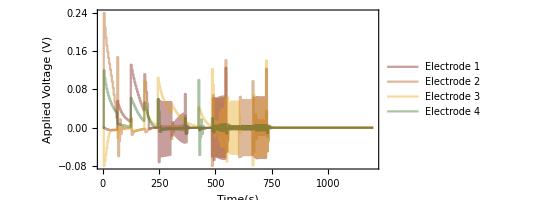

```mathematica
p3=ListPlot[Table[MapThread[{#1,#2}&,{timeList,dataX[[i]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Applied Voltage (V)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.8,0.75}],ImageSize->400]
```

```mathematica
plotCurrent[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC];
```

```mathematica
currentData=Table[plotCurrent[nEl,time],{time,0.1,1200,0.1}];
dataX=Table[currentData[[All,WE[[i,1]],WE[[i,2]]]],{i,Length@WE}];
```

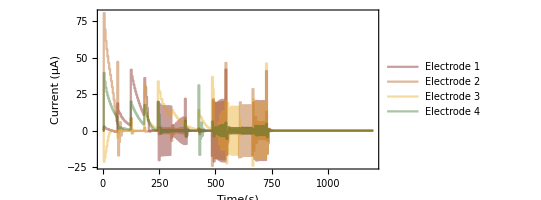

```mathematica
p4=ListPlot[Table[MapThread[{#1,10^6#2}&,{timeList,dataX[[i]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Current (μA)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.8,0.75}],ImageSize->400]
```

```mathematica
plotStyle=MapThread[{#1,#2,#3}&,{ConstantArray[PointSize[0.005],Length@CE],ConstantArray[Opacity[0.2],Length@CE],ColorData[10,#]&/@Range[Length@CE]}];
```

```mathematica
dataX=Table[currentData[[All,CE[[i,1]],CE[[i,2]]]],{i,Length@CE}];
```

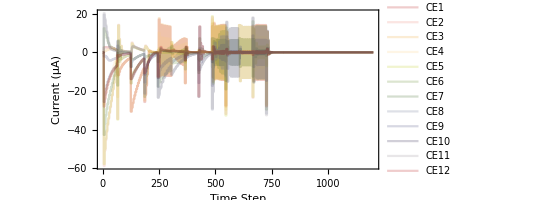

```mathematica
p5=ListPlot[Table[MapThread[{#1,10^6#2}&,{timeList,dataX[[i]]}],{i,Length@CE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time Step","Current (μA)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[Table["CE"<>ToString[el],{el,Length@CE}],LabelStyle->12,LegendLayout->"Row",Spacings-> {0.15,0.1}],{0.5,0.15}],ImageSize->400]
```

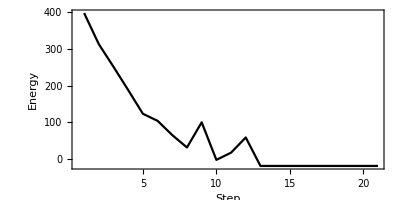

```mathematica
p6=ListPlot[energySys,Joined->True,PlotStyle->Black,Frame-> True,Axes-> None,FrameLabel-> {"Step","Energy"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,ImageSize->400]
```

```mathematica
Export[baseDirectory<>"PrimeFact_1.png",p1,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\PrimeFact_1.png

```mathematica
Export[baseDirectory<>"PrimeFact_2.png",p2,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\PrimeFact_2.png

```mathematica
Export[baseDirectory<>"PrimeFact_3.png",p3,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\PrimeFact_3.png

```mathematica
Export[baseDirectory<>"PrimeFact_4.png",p4,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\PrimeFact_4.png

```mathematica
Export[baseDirectory<>"PrimeFact_5.png",p5,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\PrimeFact_5.png

```mathematica
Export[baseDirectory<>"PrimeFact_6.png",p6,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\PrimeFact_6.png

```mathematica
BL1=BarLegend[{"TemperatureMap",{-1.,1.}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "Applied Voltage (V)",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
BL2=BarLegend[{"TemperatureMap",{-0.5,0.5}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "Electrode Current(mA)",LegendLayout->"Row",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
BL3=BarLegend[{"Pastel",{0,0.2}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "Interface Current (mA)",LegendLayout->"Row",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
BL4=BarLegend[{"LightTemperatureMap",{3,12}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "pH",LegendLayout->"Row",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
BL5=BarLegend[{"TemperatureMap",{-1,1}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "Ising States",LegendLayout->"Row",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
Export[baseDirectory<>"BL_AppliedVoltage.svg",BL1]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\BL_AppliedVoltage.svg

```mathematica
Export[baseDirectory<>"BL_ElectrodeCurrent.svg",BL2]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\BL_ElectrodeCurrent.svg

```mathematica
Export[baseDirectory<>"BL_InterfaceCurrent.svg",BL3]
```

Z:\group\0-Papers in Progress\Hybird_Computation_Abhishek\Mathematica_Notebooks\BL_InterfaceCurrent.svg

```mathematica
stateV[k_]:=ColorData[{"TemperatureMap",{-1.,1.}}][k]; (* Applied Potential *)
state[k_]:=ColorData[{"TemperatureMap",{-0.5 10^-4,0.5 10^-4}}][k]; (* Electrode Current *)
state2[k_]:=ColorData[{"Pastel",{-0.5 10^-4,0.5 10^-4}}][k]; (* Interfacial Current *)
state3[k_]:=ColorData[{"LightTemperatureMap",{-1 10^3,1 10^3}}][k]; (* Electric Field Profile *)
state4[k_]:=ColorData[{"TemperatureMap",{3,12}}][k]; (* pH profile *)
state5[k_]:= ColorData[{"TemperatureMap",{-1,1}}][k];(* Ising State +1/-1 *)
```

```mathematica
(* Plots applied voltage at a given time *)
plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl];
Graphics[Flatten@Table[{stateV[plotV⟦i,j⟧],Disk[{2i,2j},0.45],Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Applied Potential",FontSize->14,FontColor->Black]]]];
```

```mathematica
(* Plots electrode current magnitude at a given time *)
plotCurrent[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC;
Graphics[Flatten@Table[{state[currentEL⟦i,j⟧],Disk[{2i,2j},0.45](* Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}] *),Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
(* Plots interfacial current magnitude at a given time *)
plotCurrentCon[nEl_,tC_]:=Block[{cnT, time,dataPlot,dataPlot2,dataPlot3},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
dataPlot2=(Table[{1,j,Symbol["iCW1"<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{j,nEl}])/.t-> tC;
dataPlot3=(Table[{i,1,Symbol["iCS"<>ToString[i]<>"s"<>"1"][t] }/.solnS⟦cnT⟧,{i,nEl}])/.t-> tC;
Graphics[Flatten[{Table[{state2[Abs[dataPlot⟦i,3⟧]],Rectangle[{1+2dataPlot⟦i,1⟧-0.45,2dataPlot⟦i,2⟧-0.45},{1+2dataPlot⟦i,1⟧+0.45,2dataPlot⟦i,2⟧+0.45}],state2[Abs[dataPlot⟦i,4⟧]],Rectangle[{2dataPlot⟦i,1⟧-0.45,1+2dataPlot⟦i,2⟧-0.45},{2dataPlot⟦i,1⟧+0.45,1+2dataPlot⟦i,2⟧+0.45}]},{i,1,nEl^2}],Table[{state2[Abs[dataPlot2⟦i,3⟧]],Rectangle[{2dataPlot2⟦i,1⟧-0.45-1,2dataPlot2⟦i,2⟧-0.45},{2dataPlot2⟦i,1⟧+0.45-1,2dataPlot2⟦i,2⟧+0.45}]},{i,1,nEl}],Table[{state2[Abs[dataPlot3⟦i,3⟧]],Rectangle[{1+2dataPlot3⟦i,1⟧-0.45-1,2dataPlot3⟦i,2⟧-0.45-1},{1+2dataPlot3⟦i,1⟧+0.45-1,2dataPlot3⟦i,2⟧+0.45-1}]},{i,1,nEl}]}],PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]],ImageSize->300]];
```

```mathematica
(* Plots current/electric fields vectors at a given time *)
plotCurrentVec[nEl_,tC_,color_]:=Block[{cnT, time,dataPlot,dataPlot2,dataPlot3},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
dataPlot2=(Table[{1,j,Symbol["iCW1"<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{j,nEl}])/.t-> tC;
dataPlot3=(Table[{i,1,Symbol["iCS"<>ToString[i]<>"s"<>"1"][t]}/.solnS⟦cnT⟧,{i,nEl}])/.t-> tC;
Graphics[Flatten@{color,If[dataPlot⟦#,3⟧≥0,Arrow[{{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧}}],Arrow[{{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧}}]]&/@Range[nEl^2],
If[dataPlot⟦#,4⟧≥0,Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45}}],Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45}}]]&/@Range[nEl^2],
If[dataPlot2⟦#,3⟧≥0,Arrow[{{2dataPlot2⟦#,1⟧-0.45-1,2dataPlot2⟦#,2⟧},{2dataPlot2⟦#,1⟧+0.45-1,2dataPlot2⟦#,2⟧}}],Arrow[{{2dataPlot2⟦#,1⟧+0.45-1,2dataPlot2⟦#,2⟧},{2dataPlot2⟦#,1⟧-0.45-1,2dataPlot2⟦#,2⟧}}]]&/@Range[nEl],
If[dataPlot3⟦#,3⟧≥0,Arrow[{{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧-0.45-1},{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧+0.45-1}}],Arrow[{{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧+0.45-1},{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧-0.45-1}}]]&/@Range[nEl]
},ImageSize->300]];
```

```mathematica
(* Plots electric field at the interface at the given time *)
plotEFieldVec[nEl_,tC_]:=Block[{cnT, time,dataPlot,dataPlot2,dataPlot3,AreaF,connectArea,σ},
AreaF=0.3; (* Area Factor to consider the effect of interface *)
connectArea=AreaF QuantityMagnitude@UnitConvert[dropHeight^2,"m^2"];
σ=QuantityMagnitude@BulkCond;
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,1/σ 1/connectArea Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],1/σ 1/connectArea Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
dataPlot2=(Table[{1,j,1/σ 1/connectArea Symbol["iCW1"<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{j,nEl}])/.t-> tC;
dataPlot3=(Table[{i,1,1/σ 1/connectArea Symbol["iCS"<>ToString[i]<>"s"<>"1"][t] }/.solnS⟦cnT⟧,{i,nEl}])/.t-> tC;
Graphics[Flatten@{Table[{state3[Abs[dataPlot⟦i,3⟧]],Rectangle[{1+2dataPlot⟦i,1⟧-0.45,2dataPlot⟦i,2⟧-0.45},{1+2dataPlot⟦i,1⟧+0.45,2dataPlot⟦i,2⟧+0.45}],state3[Abs[dataPlot⟦i,4⟧]],Rectangle[{2dataPlot⟦i,1⟧-0.45,1+2dataPlot⟦i,2⟧-0.45},{2dataPlot⟦i,1⟧+0.45,1+2dataPlot⟦i,2⟧+0.45}]},{i,1,nEl^2}],Table[{state3[Abs[dataPlot2⟦i,3⟧]],Rectangle[{2dataPlot2⟦i,1⟧-0.45-1,2dataPlot2⟦i,2⟧-0.45},{2dataPlot2⟦i,1⟧+0.45-1,2dataPlot2⟦i,2⟧+0.45}]},{i,1,nEl}],Table[{state3[Abs[dataPlot3⟦i,3⟧]],Rectangle[{1+2dataPlot3⟦i,1⟧-0.45-1,2dataPlot3⟦i,2⟧-0.45-1},{1+2dataPlot3⟦i,1⟧+0.45-1,2dataPlot3⟦i,2⟧+0.45-1}]},{i,1,nEl}],Table[{Black,Circle[{2i,2j},0.45],Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}]},FrameTicks-> None,Frame-> True,PlotLabel->Text[Style["Electric Field",FontSize->14,FontColor->Black]],ImageSize->300]];
```

```mathematica
(*Plots pH of the droplets at a given time,fixed time step 0.1s*)plotpH[tC_]:=Block[{data},data=Flatten[Table[dataT⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧⟦i,All,1⟧,{i,1,nSteps}],1]&/@Range[Length[WE]];
Graphics[Flatten[{Table[{state4[data⟦i,tC⟧],Disk[{2 WE⟦i,1⟧,2 WE⟦i,2⟧},0.45],Black,Circle[{2 WE⟦i,1⟧,2 WE⟦i,2⟧},0.9]},{i,Length[WE]}],Table[{Black,Circle[{2 i,2 j},0.45],Black,Circle[{2 i,2 j},0.9]},{i,nEl},{j,nEl}]}],ImageSize->300,Frame->True,FrameTicks->None,PlotLabel->Text[Style["pH ",FontSize->14,FontColor->Black]]]]
```

```mathematica
plotAbstractState[tC_]:=Block[{data,dataX},data=Flatten[Table[dataT⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧⟦i,All,1⟧,{i,1,nSteps}],1]&/@Range[Length[WE]];
dataX=(-1+2/(pHStateMax-pHStateMin) (#-pHStateMin))&/@data;Graphics[Flatten[{Table[{state5[dataX⟦i,tC⟧],Disk[{2 WE⟦i,1⟧,2 WE⟦i,2⟧},0.45],Black,Circle[{2 WE⟦i,1⟧,2 WE⟦i,2⟧},0.9]},{i,Length[WE]}],Table[{Black,Circle[{2 i,2 j},0.45],Black,Circle[{2 i,2 j},0.9]},{i,nEl},{j,nEl}]}],ImageSize->300,Frame->True,FrameTicks->None,PlotLabel->Text[Style["Abstract state ",FontSize->14,FontColor->Black]]]]
```

```mathematica
plot[nEl_,t_]:=GraphicsGrid[Partition[{plotVoltage[nEl,t],Show[{plotCurrentCon[nEl,t],plotCurrent[nEl,t]},Frame->True,FrameTicks->None],plotpH[IntegerPart[t/timeStep]],plotAbstractState[IntegerPart[t/timeStep]]},2],Frame->All,PlotLabel->Text[Style["Time:"<>ToString[t],FontSize->14,FontColor->Black]],ImageSize->400]
```

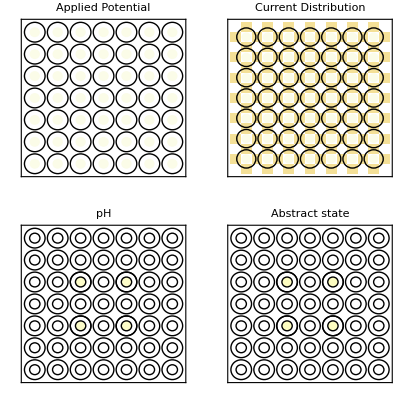

```mathematica
plot[nEl,1.5]
```

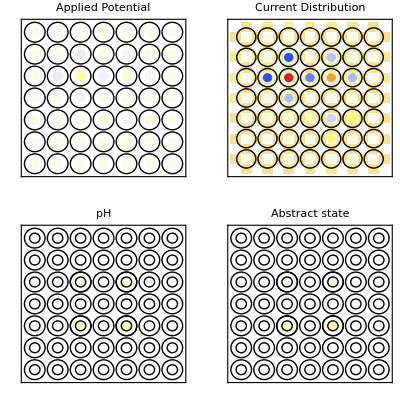

```mathematica
plot[nEl,12]
```

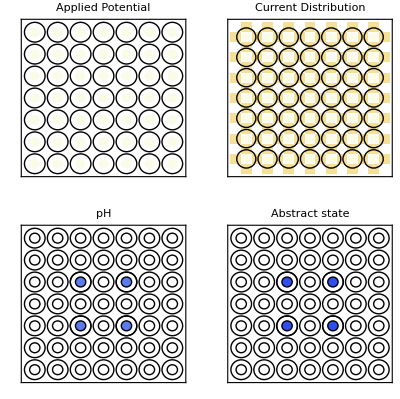

-Graphics-

```mathematica
plot[nEl,1200]
```